```mathematica
c1=1-Khh^2*Kll^2;
c2=(Khh+Ki+Kll-2*Khh*Kll)^2/(Khh^2*Kll^2-1)-Khh^2*Kll^2+1;
c3=(Khh+Ki+Kll-2*Khh*Kll)^2/(Khh^2*Kll^2-1)-(Khh+Kll-((Khh*Kll*(Khh+Ki+Kll)-2)*(Khh+Ki+Kll-2*Khh*Kll))/(Khh^2*Kll^2-1)-Khh*Kll*(Khh+Kll+1)+1)^2/((Khh+Ki+Kll-2*Khh*Kll)^2/(Khh^2*Kll^2-1)-Khh^2*Kll^2+1)-Khh^2*Kll^2+1;
c4=-(Khh^5*Kll^5+Khh^5*Kll^4-2*Khh^5*Kll^3-2*Khh^4*Ki*Kll^3+2*Khh^4*Ki*Kll^2+Khh^4*Kll^5-2*Khh^4*Kll^4-4*Khh^4*Kll^3+7*Khh^4*Kll^2-2*Khh^4*Kll-Khh^3*Ki^2*Kll^3+Khh^3*Ki^2*Kll^2-2*Khh^3*Ki*Kll^4+2*Khh^3*Ki*Kll^3+10*Khh^3*Ki*Kll^2-12*Khh^3*Ki*Kll+2*Khh^3*Ki-2*Khh^3*Kll^5-4*Khh^3*Kll^4+3*Khh^3*Kll^3+5*Khh^3*Kll^2-2*Khh^3*Kll+Khh^2*Ki^2*Kll^3+Khh^2*Ki^2*Kll^2-10*Khh^2*Ki^2*Kll+5*Khh^2*Ki^2+2*Khh^2*Ki*Kll^4+10*Khh^2*Ki*Kll^3-6*Khh^2*Ki*Kll^2-8*Khh^2*Ki*Kll+2*Khh^2*Ki+7*Khh^2*Kll^4+5*Khh^2*Kll^3-16*Khh^2*Kll^2+4*Khh^2*Kll-2*Khh*Ki^3*Kll+4*Khh*Ki^3-10*Khh*Ki^2*Kll^2+Khh*Ki^2*Kll+3*Khh*Ki^2-12*Khh*Ki*Kll^3-8*Khh*Ki*Kll^2+24*Khh*Ki*Kll-4*Khh*Ki-2*Khh*Kll^4-2*Khh*Kll^3+4*Khh*Kll^2+Ki^4+4*Ki^3*Kll+2*Ki^3+5*Ki^2*Kll^2+3*Ki^2*Kll-8*Ki^2+2*Ki*Kll^3+2*Ki*Kll^2-4*Ki*Kll)/(Khh^3*Kll^3+Khh^3*Kll^2+Khh^2*Kll^3+2*Khh^2*Kll^2-2*Khh^2*Kll+Khh^2-2*Khh*Ki*Kll+2*Khh*Ki-2*Khh*Kll^2-3*Khh*Kll+Khh+Ki^2+2*Ki*Kll+2*Ki+Kll^2+Kll-2)//FullSimplify

R1=c1>0&&c2>0&&c3>0&&c4>0;
RegionPlot3D[R1,{Khh,-1.1,1.1},{Kll,-1.1,1.1},{Ki,-0.5,0.5},AxesLabel->Automatic,FaceGrids->None,PlotPoints->35]
```

-(((Ki-Khh Kll) (4+Ki+2 Kll+Khh (2+Kll)) (-2 Ki-Kll-Khh^3 (-1+Kll) Kll^2+(Ki+Kll)^2-Khh (-1+Kll) (-1+2 Ki+4 Kll)+Khh^2 (-1+Kll) (-1+Kll (3+Kll))))/(-2+Khh+Khh^2+2 Ki-2 Khh Ki (-1+Kll)+Kll+Khh^3 Kll^2 (1+Kll)+(Ki+Kll)^2-Khh Kll (3+2 Kll)+Khh^2 Kll (-2+Kll (2+Kll))))

-Graphics3D-

```mathematica
R2=Khh>0&&Kll>0&&Ki>=0;
PP=RegionPlot3D[R1&&R2,{Khh,0,1.1},{Kll,0,1.1},{Ki,0,0.5},FaceGrids->None,PlotPoints->35]
```

-Graphics3D-

```mathematica
RegionPlot3D[R1&&R2,{Khh,0,1.1},{Kll,0,1.1},{Ki,0,0.5},FaceGrids->None,PlotPoints->35,ColorFunction->Hue]
```

-Graphics3D-

```mathematica
RegionPlot3D[R1&&R2,{Khh,0,1.1},{Kll,0,1.1},{Ki,0,0.5},FaceGrids->None,PlotPoints->35,ColorFunction->Hue,ViewPoint->{0, 0, 2}*1000]
```

-Graphics3D-

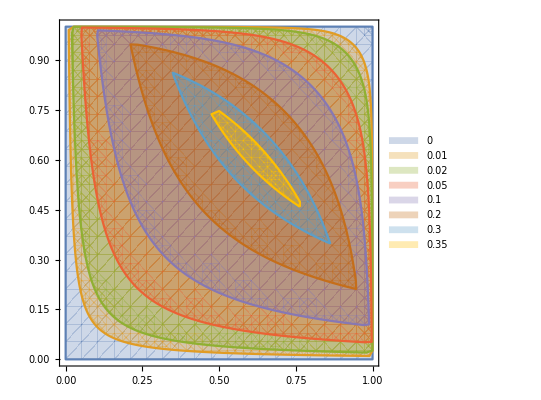

```mathematica
RegionPlot[{R1&&R2//.{Ki->0},R1&&R2//.{Ki->0.01},R1&&R2//.{Ki->0.02},R1&&R2//.{Ki->0.05},R1&&R2//.{Ki->0.1},R1&&R2//.{Ki->0.2},R1&&R2//.{Ki->0.3},R1&&R2//.{Ki->0.35}},{Khh,0,1},{Kll,0,1},PlotLegends->{0,0.01,0.02,0.05,0.1,0.2,0.3,0.35}]
```